# Reference papers

## Perturbative Gadgets at Arbitrary Orders

## Stephen P. Jordan and Edward Farhi

```mathematica
$Assumptions=λ∈Reals;
$Assumptions=λ>0;
```

```mathematica
II := IdentityMatrix[2]
X:=PauliMatrix[1]
Y:=PauliMatrix[2]
Z := PauliMatrix[3]
```

## "All-Z" example

### By hand for n = 2

```mathematica
(*s:=(-1)^(2+1)*)
s:=1
k:=2
Hcomp:=KroneckerProduct[Z,Z]
Hgad := s((1/2)*KroneckerProduct[II, II, II, II]-(1/2)*KroneckerProduct[II, II, Z, Z]+λ*KroneckerProduct[Z, II, X, II]+λ*KroneckerProduct[II, Z, II, X])
```

```mathematica
Hgad//MatrixForm
```

(0 | λ | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
λ | 1 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
λ | 0 | 1 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | λ | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -λ | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -λ | 1 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | λ | 0 | 1 | -λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | λ | -λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | -λ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 1 | 0 | -λ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 1 | λ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | λ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | -λ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 1 | 0 | -λ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 1 | -λ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | -λ | 0)

```mathematica
Eigenvalues[Hgad]
```

{1,1,1,1,0,0,0,0,1/2 (1-√(1+16 λ^2)),1/2 (1-√(1+16 λ^2)),1/2 (1-√(1+16 λ^2)),1/2 (1-√(1+16 λ^2)),1/2 (1+√(1+16 λ^2)),1/2 (1+√(1+16 λ^2)),1/2 (1+√(1+16 λ^2)),1/2 (1+√(1+16 λ^2))}

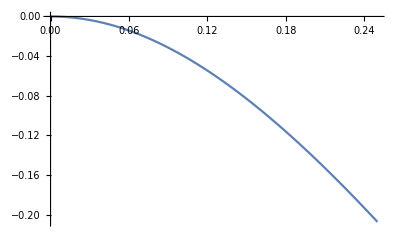

```mathematica
Plot[1/2 (1-√(1+16 λ^2)),{λ,0,0.25}]
```

```mathematica
Eigenvectors[Hgad][[9]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,1,-(1-√(1+16 λ^2))/(4 λ),-(1-√(1+16 λ^2))/(4 λ),1}

```mathematica
Norm[Eigenvectors[Hgad][[9]]]
```

√(2+1/8 Abs[(1-√(1+16 λ^2))/λ]^2)

```mathematica
Hgad00:=(1/2)*KroneckerProduct[II, II]-(1/2)*KroneckerProduct[Z, Z]+(λ)*KroneckerProduct[X, II]+(λ)*KroneckerProduct[II, X]
Hgad01:=(1/2)*KroneckerProduct[II, II]-(1/2)*KroneckerProduct[Z, Z]+(λ)*KroneckerProduct[X, II]-(λ)*KroneckerProduct[II, X]
Hgad10:=(1/2)*KroneckerProduct[II, II]-(1/2)*KroneckerProduct[Z, Z]-(λ)*KroneckerProduct[X, II]+(λ)*KroneckerProduct[II, X]
Hgad11:=(1/2)*KroneckerProduct[II, II]-(1/2)*KroneckerProduct[Z, Z]-(λ)*KroneckerProduct[X, II]-(λ)*KroneckerProduct[II, X]
```

```mathematica
Eigenvalues[Hgad00]
Eigenvalues[Hgad01]
Eigenvalues[Hgad10]
Eigenvalues[Hgad11]
```

{1,0,1/2 (1-√(1+16 λ^2)),1/2 (1+√(1+16 λ^2))}

{1,0,1/2 (1-√(1+16 λ^2)),1/2 (1+√(1+16 λ^2))}

{1,0,1/2 (1-√(1+16 λ^2)),1/2 (1+√(1+16 λ^2))}

«1 more identical outputs»

```mathematica
Eigenvectors[Hgad00]
Eigenvectors[Hgad01]
Eigenvectors[Hgad10]
Eigenvectors[Hgad11]
```

{{0,-1,1,0},{-1,0,0,1},{1,-(-1+√(1+16 λ^2))/(4 λ),-(-1+√(1+16 λ^2))/(4 λ),1},{1,-(-1-√(1+16 λ^2))/(4 λ),-(-1-√(1+16 λ^2))/(4 λ),1}}

{{0,1,1,0},{1,0,0,1},{-1,-(-1+√(1+16 λ^2))/(4 λ),-(1-√(1+16 λ^2))/(4 λ),1},{-1,-(-1-√(1+16 λ^2))/(4 λ),-(1+√(1+16 λ^2))/(4 λ),1}}

{{0,1,1,0},{1,0,0,1},{-1,-(1-√(1+16 λ^2))/(4 λ),-(-1+√(1+16 λ^2))/(4 λ),1},{-1,-(1+√(1+16 λ^2))/(4 λ),-(-1-√(1+16 λ^2))/(4 λ),1}}

{{0,-1,1,0},{-1,0,0,1},{1,-(1-√(1+16 λ^2))/(4 λ),-(1-√(1+16 λ^2))/(4 λ),1},{1,-(1+√(1+16 λ^2))/(4 λ),-(1+√(1+16 λ^2))/(4 λ),1}}

```mathematica
Limit[(-1+√(1+16 λ^2))/(4 λ),λ->0]
Limit[(1+√(1+16 λ^2))/(4 λ),λ->0]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

0

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

Indeterminate

```mathematica
Hgad.{0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0}
```

{0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0}

### By hand for n = 3

```mathematica
Hgad := (3/2)*KroneckerProduct[II, II, II, II, II, II]-(1/2)*KroneckerProduct[II, II, II, Z, Z, II]-(1/2)*KroneckerProduct[II, II, II, Z, II, Z]-(1/2)*KroneckerProduct[II, II, II, II, Z, Z]+λ*KroneckerProduct[Z, II, II, X, II, II]+λ*KroneckerProduct[II, Z, II, II, X, II]+λ*KroneckerProduct[II, II, Z, II, II, X]
```

```mathematica
Hgad[[1;;2^(5),1;;2^(5)]]//MatrixForm
```

(0 | λ | λ | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
λ | 2 | 0 | λ | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
λ | 0 | 2 | λ | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | λ | λ | 2 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
λ | 0 | 0 | 0 | 2 | λ | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | λ | 0 | 0 | λ | 2 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | λ | 0 | λ | 0 | 2 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | λ | 0 | λ | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | λ | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 2 | 0 | λ | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 2 | -λ | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | -λ | 2 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 2 | -λ | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | -λ | 2 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | λ | 0 | 2 | -λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | λ | -λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | -λ | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 2 | 0 | -λ | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 2 | λ | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | λ | 2 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 2 | λ | -λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | λ | 2 | 0 | -λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | -λ | 0 | 2 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | -λ | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | -λ | 0 | λ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 2 | 0 | -λ | 0 | λ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 2 | -λ | 0 | 0 | λ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | -λ | 2 | 0 | 0 | 0 | λ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 2 | -λ | -λ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | -λ | 2 | 0 | -λ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | -λ | 0 | 2 | -λ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | -λ | -λ | 0)

```mathematica
Eigenvalues[Hgad]
```

{2-λ,2-λ,2-λ,2-λ,2-λ,2-λ,2-λ,2-λ,2-λ,2-λ,2-λ,2-λ,2-λ,2-λ,2-λ,2-λ,2+λ,2+λ,2+λ,2+λ,2+λ,2+λ,2+λ,2+λ,2+λ,2+λ,2+λ,2+λ,2+λ,2+λ,2+λ,2+λ,1-λ-√(1-2 λ+4 λ^2),1-λ-√(1-2 λ+4 λ^2),1-λ-√(1-2 λ+4 λ^2),1-λ-√(1-2 λ+4 λ^2),1-λ-√(1-2 λ+4 λ^2),1-λ-√(1-2 λ+4 λ^2),1-λ-√(1-2 λ+4 λ^2),1-λ-√(1-2 λ+4 λ^2),1-λ+√(1-2 λ+4 λ^2),1-λ+√(1-2 λ+4 λ^2),1-λ+√(1-2 λ+4 λ^2),1-λ+√(1-2 λ+4 λ^2),1-λ+√(1-2 λ+4 λ^2),1-λ+√(1-2 λ+4 λ^2),1-λ+√(1-2 λ+4 λ^2),1-λ+√(1-2 λ+4 λ^2),1+λ-√(1+2 λ+4 λ^2),1+λ-√(1+2 λ+4 λ^2),1+λ-√(1+2 λ+4 λ^2),1+λ-√(1+2 λ+4 λ^2),1+λ-√(1+2 λ+4 λ^2),1+λ-√(1+2 λ+4 λ^2),1+λ-√(1+2 λ+4 λ^2),1+λ-√(1+2 λ+4 λ^2),1+λ+√(1+2 λ+4 λ^2),1+λ+√(1+2 λ+4 λ^2),1+λ+√(1+2 λ+4 λ^2),1+λ+√(1+2 λ+4 λ^2),1+λ+√(1+2 λ+4 λ^2),1+λ+√(1+2 λ+4 λ^2),1+λ+√(1+2 λ+4 λ^2),1+λ+√(1+2 λ+4 λ^2)}

### By hand for n = 4

```mathematica
Hgad := (6/2)*KroneckerProduct[II, II, II, II, II, II, II, II]-(1/2)*KroneckerProduct[II, II, II, II, Z, Z, II, II]-(1/2)*KroneckerProduct[II, II, II, II, Z, II, Z, II]-(1/2)*KroneckerProduct[II, II, II, II, Z, II, II, Z]-(1/2)*KroneckerProduct[II, II, II, II, II, Z, Z, II]-(1/2)*KroneckerProduct[II, II, II, II, II, Z, II, Z]-(1/2)*KroneckerProduct[II, II, II, II, II, II, Z, Z]+λ*KroneckerProduct[Z, II, II, II, X, II, II, II]+λ*KroneckerProduct[II, Z, II, II, II, X, II, II]+λ*KroneckerProduct[II, II, Z, II, II, II, X, II]+λ*KroneckerProduct[II, II, II, Z, II, II, II, X]
```

```mathematica
Hgad[[1;;2^(5),1;;2^(5)]]//MatrixForm
```

(0 | λ | λ | 0 | λ | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
λ | 3 | 0 | λ | 0 | λ | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
λ | 0 | 3 | λ | 0 | 0 | λ | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | λ | λ | 4 | 0 | 0 | 0 | λ | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
λ | 0 | 0 | 0 | 3 | λ | λ | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | λ | 0 | 0 | λ | 4 | 0 | λ | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | λ | 0 | λ | 0 | 4 | λ | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | λ | 0 | λ | λ | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | λ | λ | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | λ | 4 | 0 | λ | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | λ | 0 | 4 | λ | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | λ | λ | 3 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | λ | 0 | 0 | 0 | 4 | λ | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | λ | 0 | 0 | λ | 3 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | λ | 0 | λ | 0 | 3 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | λ | 0 | λ | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | λ | 0 | λ | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 3 | 0 | λ | 0 | λ | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 3 | -λ | 0 | 0 | λ | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | -λ | 4 | 0 | 0 | 0 | λ | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 3 | -λ | λ | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | -λ | 4 | 0 | λ | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | λ | 0 | 4 | -λ | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | λ | -λ | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | -λ | λ | 0 | λ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 4 | 0 | λ | 0 | λ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | λ | 0 | 4 | -λ | 0 | 0 | λ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | 0 | 0 | λ | -λ | 3 | 0 | 0 | 0 | λ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | λ | 0 | 0 | 0 | 4 | -λ | λ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | λ | 0 | 0 | -λ | 3 | 0 | λ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | λ | 0 | λ | 0 | 3 | -λ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 0 | 0 | 0 | λ | 0 | λ | -λ | 0)

```mathematica
$Assumptions=True;
```

## Other (non - commuting) example

### for n = 2

Choosing an example where Hcomp and Hgad do not commute, so we don’t expect a simple block structure

```mathematica
Hcomp:=KroneckerProduct[Z,Z]+KroneckerProduct[Z,X]
Hgad := (2/2)*KroneckerProduct[II, II, II, II, II, II]-(1/2)*KroneckerProduct[II, II, Z, Z, II, II]-(1/2)*KroneckerProduct[II, II, II, II, Z, Z]+λ*KroneckerProduct[Z, II, X, II, II, II]+λ*KroneckerProduct[II, Z, II, X, II, II]+λ*KroneckerProduct[Z, II, II, II, X, II]+λ*KroneckerProduct[II, X, II, II, II, X]
```

```mathematica
Hgad//MatrixForm
```

```mathematica
Assuming [λ<0.25,{Eigenvalues[Hgad]}]
```

```mathematica
Xanc:=KroneckerProduct[II, II, II, II, X, X]
U:=Eigenvectors[Xanc]
Print["Number of qubits : ", Log2[Dimensions[Hgad]⟦1⟧]]
Print["Block size : ", Log2[16], " qubits"]
(*U.Hgad.Transpose[U]//MatrixForm*)
(U.Hgad.Transpose[U])⟦1;;2^(4),1;;2^(4)⟧//MatrixForm
```

Number of qubits : 6

Block size : 4 qubits

(0 | 2 λ | -2 λ | 0 | -2 λ | 0 | 0 | 0 | 0 | 2 λ | 0 | 0 | 0 | 0 | 0 | 0
2 λ | 2 | 0 | -2 λ | 0 | -2 λ | 0 | 0 | 2 λ | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 λ | 0 | 2 | 2 λ | 0 | 0 | -2 λ | 0 | 0 | 0 | 0 | 2 λ | 0 | 0 | 0 | 0
0 | -2 λ | 2 λ | 4 | 0 | 0 | 0 | -2 λ | 0 | 0 | 2 λ | 0 | 0 | 0 | 0 | 0
-2 λ | 0 | 0 | 0 | 2 | 2 λ | -2 λ | 0 | 0 | 0 | 0 | 0 | 0 | 2 λ | 0 | 0
0 | -2 λ | 0 | 0 | 2 λ | 4 | 0 | -2 λ | 0 | 0 | 0 | 0 | 2 λ | 0 | 0 | 0
0 | 0 | -2 λ | 0 | -2 λ | 0 | 0 | 2 λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 λ
0 | 0 | 0 | -2 λ | 0 | -2 λ | 2 λ | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 2 λ | 0
0 | 2 λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 λ | 2 λ | 0 | -2 λ | 0 | 0 | 0
2 λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 λ | 2 | 0 | 2 λ | 0 | -2 λ | 0 | 0
0 | 0 | 0 | 2 λ | 0 | 0 | 0 | 0 | 2 λ | 0 | 2 | 2 λ | 0 | 0 | -2 λ | 0
0 | 0 | 2 λ | 0 | 0 | 0 | 0 | 0 | 0 | 2 λ | 2 λ | 4 | 0 | 0 | 0 | -2 λ
0 | 0 | 0 | 0 | 0 | 2 λ | 0 | 0 | -2 λ | 0 | 0 | 0 | 2 | 2 λ | 2 λ | 0
0 | 0 | 0 | 0 | 2 λ | 0 | 0 | 0 | 0 | -2 λ | 0 | 0 | 2 λ | 4 | 0 | 2 λ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 λ | 0 | 0 | -2 λ | 0 | 2 λ | 0 | 0 | 2 λ
0 | 0 | 0 | 0 | 0 | 0 | 2 λ | 0 | 0 | 0 | 0 | -2 λ | 0 | 2 λ | 2 λ | 2)

## Eigenstates of Π_0X^kΠ_0

```mathematica
k:=3
dim := 2^k
first=ConstantArray[0,dim];
first⟦1⟧=1;
last=ConstantArray[0,dim];
last⟦dim⟧=1;
P=Outer[Times,first, last]+Outer[Times, last,first];
Eigenvalues[P]
Eigenvectors[P]
```

{-1,1,0,0,0,0,0,0}

{{-1,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,1,0,0,0,0,0,0}}

## Shifted gadgets

```mathematica
Clear[λ]
k:=2
s:=(-1)^(k+1)
Hcomp:=KroneckerProduct@@Table[Z,{x,k}]
Hgad := s((2/2)*KroneckerProduct[II, II, II, II, II, II]-(1/2)*KroneckerProduct[II, II, Z, Z, II, II]-(1/2)*KroneckerProduct[II, II, II, II, Z, Z]+λ*KroneckerProduct[Z, II, X, II, II, II]+λ*KroneckerProduct[II, Z, II, X, II, II]-λ*2*KroneckerProduct[II, II, II, II, X, II]-λ*2*KroneckerProduct[II, II, II, II, II, X])
(*Hgad := (6/2)*KroneckerProduct[II, II, II, II, II, II, II, II]-(1/2)*KroneckerProduct[II, II, II, II, Z, Z, II, II]-(1/2)*KroneckerProduct[II, II, II, II, Z, II, Z, II]-(1/2)*KroneckerProduct[II, II, II, II, Z, II, II, Z]-(1/2)*KroneckerProduct[II, II, II, II, II, Z, Z, II]-(1/2)*KroneckerProduct[II, II, II, II, II, Z, II, Z]-(1/2)*KroneckerProduct[II, II, II, II, II, II, Z, Z]+λ*KroneckerProduct[Z, II, II, II, X, II, II, II]+λ*KroneckerProduct[II, Z, II, II, II, X, II, II]+λ*KroneckerProduct[II, II, Z, II, II, II, X, II]+λ*KroneckerProduct[II, II, II, Z, II, II, II, X]*)
```

```mathematica
Hgad//MatrixForm
```

```mathematica
λ:=(1/2)*(k-1)/(4k)
{e,v}=Eigensystem[Hgad];
Min[e]
Sort[e]
```

1/4 (-4-√17)

{-2,-2,-2,-2,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,0,0,0,1/8 (-12-√17),1/8 (-12-√17),1/8 (-12-√17),1/8 (-12-√17),1/8 (-12-√17),1/8 (-12-√17),1/8 (-12-√17),1/8 (-12-√17),1/8 (-4-√17),1/8 (-4-√17),1/8 (-4-√17),1/8 (-4-√17),1/8 (-4-√17),1/8 (-4-√17),1/8 (-4-√17),1/8 (-4-√17),1/4 (-4-√17),1/4 (-4-√17),1/4 (-4-√17),1/4 (-4-√17),1/8 (-12+√17),1/8 (-12+√17),1/8 (-12+√17),1/8 (-12+√17),1/8 (-12+√17),1/8 (-12+√17),1/8 (-12+√17),1/8 (-12+√17),1/8 (-4+√17),1/8 (-4+√17),1/8 (-4+√17),1/8 (-4+√17),1/8 (-4+√17),1/8 (-4+√17),1/8 (-4+√17),1/8 (-4+√17),1/4 (-4+√17),1/4 (-4+√17),1/4 (-4+√17),1/4 (-4+√17)}

```mathematica
nblock:=2^4
Hgad[[1;;nblock,1;;nblock]]//MatrixForm
BaseForm[nblock-1,2]
```

(0 | λ | λ | 0 | -λ | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0 | 0 | 0 | 0
λ | -1 | 0 | λ | 0 | -λ | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0 | 0 | 0
λ | 0 | -1 | λ | 0 | 0 | -λ | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0 | 0
0 | λ | λ | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0
-λ | 0 | 0 | 0 | -1 | λ | λ | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0
0 | -λ | 0 | 0 | λ | -2 | 0 | λ | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0
0 | 0 | -λ | 0 | λ | 0 | -2 | λ | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0
0 | 0 | 0 | -λ | 0 | λ | λ | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ
-λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | λ | λ | 0 | -λ | 0 | 0 | 0
0 | -λ | 0 | 0 | 0 | 0 | 0 | 0 | λ | -2 | 0 | λ | 0 | -λ | 0 | 0
0 | 0 | -λ | 0 | 0 | 0 | 0 | 0 | λ | 0 | -2 | λ | 0 | 0 | -λ | 0
0 | 0 | 0 | -λ | 0 | 0 | 0 | 0 | 0 | λ | λ | -1 | 0 | 0 | 0 | -λ
0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | -λ | 0 | 0 | 0 | 0 | λ | λ | 0
0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | -λ | 0 | 0 | λ | -1 | 0 | λ
0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | -λ | 0 | λ | 0 | -1 | λ
0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 0 | 0 | 0 | -λ | 0 | λ | λ | 0)

1111_2

```mathematica
Eigenvalues[Hgad[[1;;nblock,1;;nblock]]]
Eigenvalues[Hgad[[nblock+1;;2*nblock,nblock+1;;2*nblock]]]
Eigenvalues[Hgad[[2*nblock+1;;3*nblock,2*nblock+1;;3*nblock]]]
Eigenvalues[Hgad[[3*nblock+1;;4*nblock,3*nblock+1;;4*nblock]]]
```

{-2,-1,-1,0,1/2 (-3-√(1+16 λ^2)),1/2 (-1-√(1+16 λ^2)),1/2 (-3+√(1+16 λ^2)),1/2 (-1+√(1+16 λ^2)),1/2 (-3-√(1+64 λ^2)),1/2 (-1-√(1+64 λ^2)),1/2 (-3+√(1+64 λ^2)),1/2 (-1+√(1+64 λ^2)),1/2 (-2-√2 √(1+40 λ^2-√(1+80 λ^2+1024 λ^4))),1/2 (-2+√2 √(1+40 λ^2-√(1+80 λ^2+1024 λ^4))),1/2 (-2-√2 √(1+40 λ^2+√(1+80 λ^2+1024 λ^4))),1/2 (-2+√2 √(1+40 λ^2+√(1+80 λ^2+1024 λ^4)))}

{-2,-1,-1,0,1/2 (-3-√(1+16 λ^2)),1/2 (-1-√(1+16 λ^2)),1/2 (-3+√(1+16 λ^2)),1/2 (-1+√(1+16 λ^2)),1/2 (-3-√(1+64 λ^2)),1/2 (-1-√(1+64 λ^2)),1/2 (-3+√(1+64 λ^2)),1/2 (-1+√(1+64 λ^2)),1/2 (-2-√2 √(1+40 λ^2-√(1+80 λ^2+1024 λ^4))),1/2 (-2+√2 √(1+40 λ^2-√(1+80 λ^2+1024 λ^4))),1/2 (-2-√2 √(1+40 λ^2+√(1+80 λ^2+1024 λ^4))),1/2 (-2+√2 √(1+40 λ^2+√(1+80 λ^2+1024 λ^4)))}

{-2,-1,-1,0,1/2 (-3-√(1+16 λ^2)),1/2 (-1-√(1+16 λ^2)),1/2 (-3+√(1+16 λ^2)),1/2 (-1+√(1+16 λ^2)),1/2 (-3-√(1+64 λ^2)),1/2 (-1-√(1+64 λ^2)),1/2 (-3+√(1+64 λ^2)),1/2 (-1+√(1+64 λ^2)),1/2 (-2-√2 √(1+40 λ^2-√(1+80 λ^2+1024 λ^4))),1/2 (-2+√2 √(1+40 λ^2-√(1+80 λ^2+1024 λ^4))),1/2 (-2-√2 √(1+40 λ^2+√(1+80 λ^2+1024 λ^4))),1/2 (-2+√2 √(1+40 λ^2+√(1+80 λ^2+1024 λ^4)))}

«1 more identical outputs»

```mathematica
BaseForm[#,2]&/@Table[x+3,{x,8}]
Limit[-(-1-√(1+16 λ^2))/(4 λ),λ->0]
Limit[(2 (1+6 λ^2+√(1+16 λ^2)))/(λ (5+3 √(1+16 λ^2))),λ->0]
Limit[(2 λ (1+4 λ^2-√(1+16 λ^2)))/(-1-10 λ^2+√(1+16 λ^2)+2 λ^2 √(1+16 λ^2)),λ->0]
{e,v}=Eigensystem[Hgad[[2*nblock+1;;3*nblock,2*nblock+1;;3*nblock]]];
Print[e]
Print[v]
```

{100_2,101_2,110_2,111_2,1000_2,1001_2,1010_2,1011_2}

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

Indeterminate

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

Indeterminate

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

Indeterminate

{-2,-1,-1,-1,-1,0,1/2 (-3-√(1+16 λ^2)),1/2 (-3-√(1+16 λ^2)),1/2 (-1-√(1+16 λ^2)),1/2 (-1-√(1+16 λ^2)),-1-√(1+16 λ^2),1/2 (-3+√(1+16 λ^2)),1/2 (-3+√(1+16 λ^2)),1/2 (-1+√(1+16 λ^2)),1/2 (-1+√(1+16 λ^2)),-1+√(1+16 λ^2)}

{{0,0,0,0,0,-1,1,0,0,-1,1,0,0,0,0,0},{-1,0,0,-1,0,-1,-1,-1/λ,1/λ,1,1,0,1,0,0,1},{0,-1,0,0,0,0,0,-1,1,0,0,0,0,0,1,0},{0,0,-1,0,0,0,0,-1,1,0,0,0,0,1,0,0},{0,0,0,0,-1,0,0,1,-1,0,0,1,0,0,0,0},{-1,0,0,1,0,0,0,0,0,0,0,0,-1,0,0,1},{0,1,-1,0,0,(2 (1+6 λ^2+√(1+16 λ^2)))/(λ (5+3 √(1+16 λ^2))),-(2 (1+6 λ^2+√(1+16 λ^2)))/(λ (5+3 √(1+16 λ^2))),0,0,-(2 (1+6 λ^2+√(1+16 λ^2)))/(λ (5+3 √(1+16 λ^2))),(2 (1+6 λ^2+√(1+16 λ^2)))/(λ (5+3 √(1+16 λ^2))),0,0,-1,1,0},{0,0,0,0,1,-(1+√(1+16 λ^2))/(4 λ),-(1+√(1+16 λ^2))/(4 λ),1,1,-(1+√(1+16 λ^2))/(4 λ),-(1+√(1+16 λ^2))/(4 λ),1,0,0,0,0},{1,0,0,-1,(2 λ (1+4 λ^2-√(1+16 λ^2)))/(-1-10 λ^2+√(1+16 λ^2)+2 λ^2 √(1+16 λ^2)),0,0,(2 λ (-1-4 λ^2+√(1+16 λ^2)))/(-1-10 λ^2+√(1+16 λ^2)+2 λ^2 √(1+16 λ^2)),-(2 λ (1+4 λ^2-√(1+16 λ^2)))/(-1-10 λ^2+√(1+16 λ^2)+2 λ^2 √(1+16 λ^2)),0,0,(2 λ (1+4 λ^2-√(1+16 λ^2)))/(-1-10 λ^2+√(1+16 λ^2)+2 λ^2 √(1+16 λ^2)),-1,0,0,1},{0,1,1,-(4 (-1-13 λ^2+√(1+16 λ^2)+3 λ^2 √(1+16 λ^2)))/(λ (3+24 λ^2-5 √(1+16 λ^2))),1,0,0,-1,-1,0,0,1,-(4 (-1-13 λ^2+√(1+16 λ^2)+3 λ^2 √(1+16 λ^2)))/(λ (3+24 λ^2-5 √(1+16 λ^2))),-((6912 λ^6-73728 λ^8+196608 λ^10-55296 λ^6 √(1+16 λ^2)+491520 λ^8 √(1+16 λ^2)-1048576 λ^10 √(1+16 λ^2)+175104 λ^6 (1+16 λ^2)-1187840 λ^8 (1+16 λ^2)+1703936 λ^10 (1+16 λ^2)-292864 λ^6 (1+16 λ^2)^(3/2)+1376256 λ^8 (1+16 λ^2)^(3/2)-1048576 λ^10 (1+16 λ^2)^(3/2)+285184 λ^6 (1+16 λ^2)^2-811008 λ^8 (1+16 λ^2)^2+196608 λ^10 (1+16 λ^2)^2-165888 λ^6 (1+16 λ^2)^(5/2)+229376 λ^8 (1+16 λ^2)^(5/2)+56320 λ^6 (1+16 λ^2)^3-24576 λ^8 (1+16 λ^2)^3-10240 λ^6 (1+16 λ^2)^(7/2)+768 λ^6 (1+16 λ^2)^4)/(-6912 λ^6+73728 λ^8-196608 λ^10+55296 λ^6 √(1+16 λ^2)-491520 λ^8 √(1+16 λ^2)+1048576 λ^10 √(1+16 λ^2)-175104 λ^6 (1+16 λ^2)+1187840 λ^8 (1+16 λ^2)-1703936 λ^10 (1+16 λ^2)+292864 λ^6 (1+16 λ^2)^(3/2)-1376256 λ^8 (1+16 λ^2)^(3/2)+1048576 λ^10 (1+16 λ^2)^(3/2)-285184 λ^6 (1+16 λ^2)^2+811008 λ^8 (1+16 λ^2)^2-196608 λ^10 (1+16 λ^2)^2+165888 λ^6 (1+16 λ^2)^(5/2)-229376 λ^8 (1+16 λ^2)^(5/2)-56320 λ^6 (1+16 λ^2)^3+24576 λ^8 (1+16 λ^2)^3+10240 λ^6 (1+16 λ^2)^(7/2)-768 λ^6 (1+16 λ^2)^4)),1,0},{(-1-16 λ^2+√(1+16 λ^2)+24 λ^2 √(1+16 λ^2))/(√(1+16 λ^2) (-1-24 λ^2+√(1+16 λ^2))),-(4 λ √(1+16 λ^2))/(-1-16 λ^2+√(1+16 λ^2)),-(2 λ (3+48 λ^2+√(1+16 λ^2)))/(√(1+16 λ^2) (-1-24 λ^2+√(1+16 λ^2))),(-1-16 λ^2+√(1+16 λ^2)+24 λ^2 √(1+16 λ^2))/(√(1+16 λ^2) (-1-24 λ^2+√(1+16 λ^2))),(8 λ √(1+16 λ^2) (1+18 λ^2) (1+20 λ^2+64 λ^4-√(1+16 λ^2)-12 λ^2 √(1+16 λ^2)))/((-1-24 λ^2+√(1+16 λ^2)) (-1-16 λ^2+√(1+16 λ^2)) (-1-22 λ^2-96 λ^4+√(1+16 λ^2)+14 λ^2 √(1+16 λ^2))),-(16 λ^2 √(1+16 λ^2) (1+18 λ^2) (-1-16 λ^2+√(1+16 λ^2)+8 λ^2 √(1+16 λ^2)))/((-1-24 λ^2+√(1+16 λ^2)) (-1-16 λ^2+√(1+16 λ^2)) (-1-22 λ^2-96 λ^4+√(1+16 λ^2)+14 λ^2 √(1+16 λ^2))),-(16 λ^2 √(1+16 λ^2) (1+18 λ^2) (-1-16 λ^2+√(1+16 λ^2)+8 λ^2 √(1+16 λ^2)))/((-1-24 λ^2+√(1+16 λ^2)) (-1-16 λ^2+√(1+16 λ^2)) (-1-22 λ^2-96 λ^4+√(1+16 λ^2)+14 λ^2 √(1+16 λ^2))),(2 λ √(1+16 λ^2) (1+12 λ^2-√(1+16 λ^2)))/(-1-22 λ^2-96 λ^4+√(1+16 λ^2)+14 λ^2 √(1+16 λ^2)),-(8 λ √(1+16 λ^2) (1+18 λ^2) (1+20 λ^2+64 λ^4-√(1+16 λ^2)-12 λ^2 √(1+16 λ^2)))/((-1-24 λ^2+√(1+16 λ^2)) (-1-16 λ^2+√(1+16 λ^2)) (-1-22 λ^2-96 λ^4+√(1+16 λ^2)+14 λ^2 √(1+16 λ^2))),-(32 λ^2 (1+18 λ^2) (-1-48 λ^2-768 λ^4-4096 λ^6+√(1+16 λ^2)+40 λ^2 √(1+16 λ^2)+480 λ^4 √(1+16 λ^2)+1536 λ^6 √(1+16 λ^2)))/(√(1+16 λ^2) (-1-24 λ^2+√(1+16 λ^2))^2 (-1-16 λ^2+√(1+16 λ^2)) (-1-22 λ^2-96 λ^4+√(1+16 λ^2)+14 λ^2 √(1+16 λ^2))),(16 λ^2 √(1+16 λ^2) (1+18 λ^2) (-1-16 λ^2+√(1+16 λ^2)+8 λ^2 √(1+16 λ^2)))/((-1-24 λ^2+√(1+16 λ^2)) (-1-16 λ^2+√(1+16 λ^2)) (-1-22 λ^2-96 λ^4+√(1+16 λ^2)+14 λ^2 √(1+16 λ^2))),-(2 λ √(1+16 λ^2) (1+12 λ^2-√(1+16 λ^2)))/(-1-22 λ^2-96 λ^4+√(1+16 λ^2)+14 λ^2 √(1+16 λ^2)),1,-(1+16 λ^2+√(1+16 λ^2))/(4 λ √(1+16 λ^2)),-((-128 λ^9 (1+16 λ^2)^(3/2)+32 λ^7 (1+16 λ^2)^2+384 λ^9 (1+16 λ^2)^2+8 λ^5 (1+16 λ^2)^(5/2)+128 λ^9 (1+16 λ^2)^(5/2)-2 λ^3 (1+16 λ^2)^3-40 λ^5 (1+16 λ^2)^3-320 λ^7 (1+16 λ^2)^3-384 λ^9 (1+16 λ^2)^3+4 λ^3 (1+16 λ^2)^(7/2)+16 λ^5 (1+16 λ^2)^(7/2)+10 λ^3 (1+16 λ^2)^4+112 λ^5 (1+16 λ^2)^4+288 λ^7 (1+16 λ^2)^4-8 λ^3 (1+16 λ^2)^(9/2)-24 λ^5 (1+16 λ^2)^(9/2)-14 λ^3 (1+16 λ^2)^5-72 λ^5 (1+16 λ^2)^5+4 λ^3 (1+16 λ^2)^(11/2)+6 λ^3 (1+16 λ^2)^6)/(-512 λ^10 (1+16 λ^2)^(3/2)+64 λ^6 (1+16 λ^2)^(5/2)+512 λ^8 (1+16 λ^2)^(5/2)+512 λ^10 (1+16 λ^2)^(5/2)-2 λ^2 (1+16 λ^2)^(7/2)-32 λ^4 (1+16 λ^2)^(7/2)-256 λ^6 (1+16 λ^2)^(7/2)-512 λ^8 (1+16 λ^2)^(7/2)+6 λ^2 (1+16 λ^2)^(9/2)+64 λ^4 (1+16 λ^2)^(9/2)+192 λ^6 (1+16 λ^2)^(9/2)-6 λ^2 (1+16 λ^2)^(11/2)-32 λ^4 (1+16 λ^2)^(11/2)+2 λ^2 (1+16 λ^2)^(13/2))),1},{0,1,-1,0,0,(2 (-1-6 λ^2+√(1+16 λ^2)))/(λ (-5+3 √(1+16 λ^2))),-(2 (-1-6 λ^2+√(1+16 λ^2)))/(λ (-5+3 √(1+16 λ^2))),0,0,-(2 (-1-6 λ^2+√(1+16 λ^2)))/(λ (-5+3 √(1+16 λ^2))),(2 (-1-6 λ^2+√(1+16 λ^2)))/(λ (-5+3 √(1+16 λ^2))),0,0,-1,1,0},{0,0,0,0,1,-(1-√(1+16 λ^2))/(4 λ),-(1-√(1+16 λ^2))/(4 λ),1,1,-(1-√(1+16 λ^2))/(4 λ),-(1-√(1+16 λ^2))/(4 λ),1,0,0,0,0},{1,0,0,-1,-(2 λ (1+4 λ^2+√(1+16 λ^2)))/(1+10 λ^2+√(1+16 λ^2)+2 λ^2 √(1+16 λ^2)),0,0,(2 λ (1+4 λ^2+√(1+16 λ^2)))/(1+10 λ^2+√(1+16 λ^2)+2 λ^2 √(1+16 λ^2)),(2 λ (1+4 λ^2+√(1+16 λ^2)))/(1+10 λ^2+√(1+16 λ^2)+2 λ^2 √(1+16 λ^2)),0,0,-(2 λ (1+4 λ^2+√(1+16 λ^2)))/(1+10 λ^2+√(1+16 λ^2)+2 λ^2 √(1+16 λ^2)),-1,0,0,1},{0,1,1,(4 (1+13 λ^2+√(1+16 λ^2)+3 λ^2 √(1+16 λ^2)))/(λ (3+24 λ^2+5 √(1+16 λ^2))),1,0,0,-1,-1,0,0,1,(4 (1+13 λ^2+√(1+16 λ^2)+3 λ^2 √(1+16 λ^2)))/(λ (3+24 λ^2+5 √(1+16 λ^2))),-((6912 λ^6-73728 λ^8+196608 λ^10+55296 λ^6 √(1+16 λ^2)-491520 λ^8 √(1+16 λ^2)+1048576 λ^10 √(1+16 λ^2)+175104 λ^6 (1+16 λ^2)-1187840 λ^8 (1+16 λ^2)+1703936 λ^10 (1+16 λ^2)+292864 λ^6 (1+16 λ^2)^(3/2)-1376256 λ^8 (1+16 λ^2)^(3/2)+1048576 λ^10 (1+16 λ^2)^(3/2)+285184 λ^6 (1+16 λ^2)^2-811008 λ^8 (1+16 λ^2)^2+196608 λ^10 (1+16 λ^2)^2+165888 λ^6 (1+16 λ^2)^(5/2)-229376 λ^8 (1+16 λ^2)^(5/2)+56320 λ^6 (1+16 λ^2)^3-24576 λ^8 (1+16 λ^2)^3+10240 λ^6 (1+16 λ^2)^(7/2)+768 λ^6 (1+16 λ^2)^4)/(-6912 λ^6+73728 λ^8-196608 λ^10-55296 λ^6 √(1+16 λ^2)+491520 λ^8 √(1+16 λ^2)-1048576 λ^10 √(1+16 λ^2)-175104 λ^6 (1+16 λ^2)+1187840 λ^8 (1+16 λ^2)-1703936 λ^10 (1+16 λ^2)-292864 λ^6 (1+16 λ^2)^(3/2)+1376256 λ^8 (1+16 λ^2)^(3/2)-1048576 λ^10 (1+16 λ^2)^(3/2)-285184 λ^6 (1+16 λ^2)^2+811008 λ^8 (1+16 λ^2)^2-196608 λ^10 (1+16 λ^2)^2-165888 λ^6 (1+16 λ^2)^(5/2)+229376 λ^8 (1+16 λ^2)^(5/2)-56320 λ^6 (1+16 λ^2)^3+24576 λ^8 (1+16 λ^2)^3-10240 λ^6 (1+16 λ^2)^(7/2)-768 λ^6 (1+16 λ^2)^4)),1,0},{-(1+16 λ^2+√(1+16 λ^2)+24 λ^2 √(1+16 λ^2))/(√(1+16 λ^2) (1+24 λ^2+√(1+16 λ^2))),-(4 λ √(1+16 λ^2))/(1+16 λ^2+√(1+16 λ^2)),(2 λ (-3-48 λ^2+√(1+16 λ^2)))/(√(1+16 λ^2) (1+24 λ^2+√(1+16 λ^2))),-(1+16 λ^2+√(1+16 λ^2)+24 λ^2 √(1+16 λ^2))/(√(1+16 λ^2) (1+24 λ^2+√(1+16 λ^2))),(8 λ √(1+16 λ^2) (1+18 λ^2) (1+20 λ^2+64 λ^4+√(1+16 λ^2)+12 λ^2 √(1+16 λ^2)))/((1+16 λ^2+√(1+16 λ^2)) (1+24 λ^2+√(1+16 λ^2)) (1+22 λ^2+96 λ^4+√(1+16 λ^2)+14 λ^2 √(1+16 λ^2))),(16 λ^2 √(1+16 λ^2) (1+18 λ^2) (1+16 λ^2+√(1+16 λ^2)+8 λ^2 √(1+16 λ^2)))/((1+16 λ^2+√(1+16 λ^2)) (1+24 λ^2+√(1+16 λ^2)) (1+22 λ^2+96 λ^4+√(1+16 λ^2)+14 λ^2 √(1+16 λ^2))),(16 λ^2 √(1+16 λ^2) (1+18 λ^2) (1+16 λ^2+√(1+16 λ^2)+8 λ^2 √(1+16 λ^2)))/((1+16 λ^2+√(1+16 λ^2)) (1+24 λ^2+√(1+16 λ^2)) (1+22 λ^2+96 λ^4+√(1+16 λ^2)+14 λ^2 √(1+16 λ^2))),(2 λ √(1+16 λ^2) (1+12 λ^2+√(1+16 λ^2)))/(1+22 λ^2+96 λ^4+√(1+16 λ^2)+14 λ^2 √(1+16 λ^2)),-(8 λ √(1+16 λ^2) (1+18 λ^2) (1+20 λ^2+64 λ^4+√(1+16 λ^2)+12 λ^2 √(1+16 λ^2)))/((1+16 λ^2+√(1+16 λ^2)) (1+24 λ^2+√(1+16 λ^2)) (1+22 λ^2+96 λ^4+√(1+16 λ^2)+14 λ^2 √(1+16 λ^2))),-(32 λ^2 (1+18 λ^2) (1+48 λ^2+768 λ^4+4096 λ^6+√(1+16 λ^2)+40 λ^2 √(1+16 λ^2)+480 λ^4 √(1+16 λ^2)+1536 λ^6 √(1+16 λ^2)))/(√(1+16 λ^2) (1+16 λ^2+√(1+16 λ^2)) (1+24 λ^2+√(1+16 λ^2))^2 (1+22 λ^2+96 λ^4+√(1+16 λ^2)+14 λ^2 √(1+16 λ^2))),-(16 λ^2 √(1+16 λ^2) (1+18 λ^2) (1+16 λ^2+√(1+16 λ^2)+8 λ^2 √(1+16 λ^2)))/((1+16 λ^2+√(1+16 λ^2)) (1+24 λ^2+√(1+16 λ^2)) (1+22 λ^2+96 λ^4+√(1+16 λ^2)+14 λ^2 √(1+16 λ^2))),-(2 λ √(1+16 λ^2) (1+12 λ^2+√(1+16 λ^2)))/(1+22 λ^2+96 λ^4+√(1+16 λ^2)+14 λ^2 √(1+16 λ^2)),1,-(-1-16 λ^2+√(1+16 λ^2))/(4 λ √(1+16 λ^2)),-((128 λ^9 (1+16 λ^2)^(3/2)+32 λ^7 (1+16 λ^2)^2+384 λ^9 (1+16 λ^2)^2-8 λ^5 (1+16 λ^2)^(5/2)-128 λ^9 (1+16 λ^2)^(5/2)-2 λ^3 (1+16 λ^2)^3-40 λ^5 (1+16 λ^2)^3-320 λ^7 (1+16 λ^2)^3-384 λ^9 (1+16 λ^2)^3-4 λ^3 (1+16 λ^2)^(7/2)-16 λ^5 (1+16 λ^2)^(7/2)+10 λ^3 (1+16 λ^2)^4+112 λ^5 (1+16 λ^2)^4+288 λ^7 (1+16 λ^2)^4+8 λ^3 (1+16 λ^2)^(9/2)+24 λ^5 (1+16 λ^2)^(9/2)-14 λ^3 (1+16 λ^2)^5-72 λ^5 (1+16 λ^2)^5-4 λ^3 (1+16 λ^2)^(11/2)+6 λ^3 (1+16 λ^2)^6)/(512 λ^10 (1+16 λ^2)^(3/2)-64 λ^6 (1+16 λ^2)^(5/2)-512 λ^8 (1+16 λ^2)^(5/2)-512 λ^10 (1+16 λ^2)^(5/2)+2 λ^2 (1+16 λ^2)^(7/2)+32 λ^4 (1+16 λ^2)^(7/2)+256 λ^6 (1+16 λ^2)^(7/2)+512 λ^8 (1+16 λ^2)^(7/2)-6 λ^2 (1+16 λ^2)^(9/2)-64 λ^4 (1+16 λ^2)^(9/2)-192 λ^6 (1+16 λ^2)^(9/2)+6 λ^2 (1+16 λ^2)^(11/2)+32 λ^4 (1+16 λ^2)^(11/2)-2 λ^2 (1+16 λ^2)^(13/2))),1}}